```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/user/Library/CloudStorage/OneDrive-TheUniversityofManchester/Mphys_Projects/WS_fittingwithGaussian

```mathematica
(*Parameters*)
A=10; (*Mass number of 10Be-core*)
r0=1.20*A^(1/3.) ;(*Central radius in: femtometers*)
a0=0.60; (*Surface thickness parameter: in femtometers*)
V0=-62.52; (*Depth of central potential for even-l states: in MeV*)
V1=-39.74; (*Depth of central potential for odd-l states: in MeV*)
Vls=21.00;(*Depth of spin-orbit potential: in MeV*)
```

```mathematica
(*Define the Woods-Saxon function and its derivative*)
fWS[r_]:=1/(1+Exp[(r-r0)/a0])
dfWS[r_]:=FullSimplify[fWS'[r]]
```

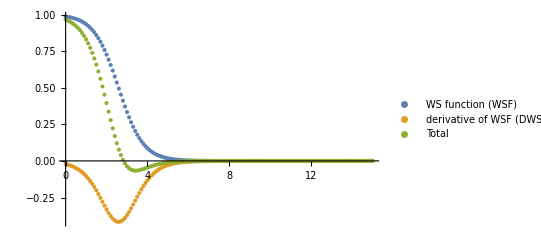

```mathematica
(*Generate a set of points to fit the Woods-Saxon function*)
dataC=Table[{r,fWS[r]},{r,0,15,0.100}];
dataSO=Table[{r,dfWS[r]},{r,0,15,0.100}];
dataT=Table[{r,(fWS[r]+dfWS[r])},{r,0,15,0.100}];
ListPlot[{dataC, dataSO,dataT}, PlotRange-> All,PlotLegends->{"WS function (WSF)", "derivative of WSF (DWSF)","Total"}]
```

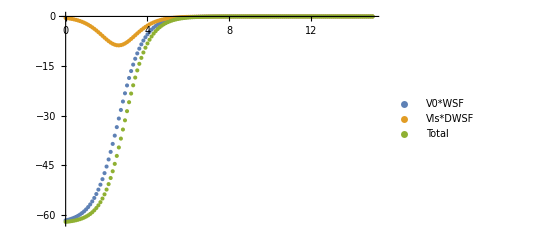

```mathematica
(*Generate a set of points multiplied with depths to fit the Woods-Saxon function gor even-l states*)
dataVC=Table[{r,V0*fWS[r]},{r,0,15,0.100}];
dataVSO=Table[{r,Vls*dfWS[r]},{r,0.,15,0.100}];
dataVT=Table[{r,(V0*fWS[r]+Vls*dfWS[r])},{r,0.0,15,0.100}];
ListPlot[{dataVC, dataVSO,dataVT}, PlotRange-> Full,PlotLegends->{"V0*WSF", "Vls*DWSF","Total"}]
```

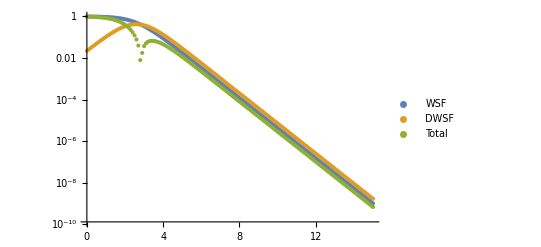

```mathematica
ListLogPlot[Abs[{dataC, dataSO,dataT}], PlotRange-> Full,PlotLegends->{"WSF", "DWSF","Total"}]
```

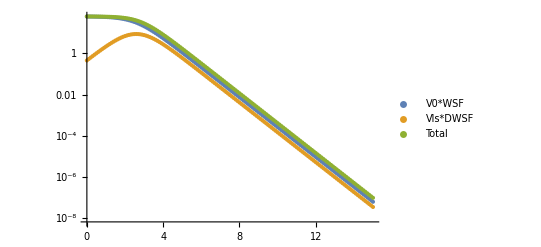

```mathematica
ListLogPlot[Abs[{dataVC, dataVSO,dataVT}], PlotRange-> Full,PlotLegends->{"V0*WSF", "Vls*DWSF","Total"}]
```

### Geometric-Function geometric[first_, last_, n_, i_]: generates a term in a geometric sequence. The function geometric provides a way to interpolate between first and last over n terms in a geometric fashion. This is particularly useful if you need a smooth progression from one value to another in multiplicative steps. Where: first: is the first term of the geometric sequence. last: is the last term of the geometric sequence. n: is the total number of terms in the sequence. i: is the index of the term we want to calculate, where 𝑖=1 corresponds to the first term, i=2 to the second term, and so on. The term Log[last/first]: calculates the logarithm of the ratio between last and first. This effectively helps in determining the common ratio for a geometric progression that would scale first to last over n terms. The expression (i - 1)/(n - 1) scales the exponent linearly based on the index i, ensuring that when i=1, the exponent is 0 (yielding first), and when i=n, the term evaluates to last. Exp[Log[last/first] (i - 1)/(n - 1)] computes the common ratio raised to the power needed to reach the i-th term. Multiplying this by first scales it back to match the desired sequence.

```mathematica
geometric[first_,last_,n_,i_]:=first Exp[Log[last/first](i-1)/(n-1)]
```

```mathematica
gaussFitCW[iMax_]:=Block[
{model=Sum[cw[i] Exp[-(r/geometric[0.49,4.0,iMax,i])^2],{i,1,iMax}]},NonlinearModelFit[{#[[1]],#[[2]]}&/@dataC,model,Join@@Table[{cw[i]},{i,iMax}],r,MaxIterations->10000,Weights->(1/Sqrt[(#[[2]])^2]&/@dataC)]
]
```

### gaussFitCW[iMax_] defines a function gaussFitC that takes iMax as an argument. iMax determines the number of terms in the sum. The Block construct is used to define a local variable model. Model is defined as a sum of Gaussian-like functions, where each term has: A coefficient c[i] (to be determined by the fit). An exponential decay term Exp[-(r / geometric[0.49, 5.3, iMax, i])^2]. NonlinearModelFit is used to fit the model to data. The data is given by {#[[1]], #[[2]]} & /@ dataC, which suggests dataC is a list of pairs {x, y} (e.g., experimental or measured data). The parameters to be optimized are {c[i]} for i = 1 to iMax. In summary This function gaussFitCW[iMax_] constructs a nonlinear sum of Gaussian-like functions and fits them to a dataset dataC. The number of terms in the sum is determined by iMax, and the parameters c[i] are optimized to best match the data. The function geometric[0.49, 5.3, iMax, i] seems to control the width or spread of each Gaussian component. Weights: Weights -> (1/Sqrt[#[[2]]^2] & /@ dataC) The weights used in the fitting process are inversely proportional to the square root of the squared y-value errors in dataC. This suggests an uncertainty-weighted fitting approach.

```mathematica
nmcw=gaussFitCW[12]
```

FittedModel[0.272822 ⅇ^(-4.16493 r^2)-1.30687 ⅇ^(-2.84325 r^2)+«12»+0.00107583 ⅇ^(-0.0625 r^2)]

```mathematica
imax=12;
tcww=Table[{i,geometric[0.49,4.0,imax,i],cw[i],1/(geometric[0.49,4.0,imax,i])^2,-62.52*cw[i]},{i,1,imax}]/.nmcw["BestFitParameters"]//TableForm
```

1 | 0.49 | 0.272822 | 4.16493 | -17.0568
2 | 0.593052 | -1.30687 | 2.84325 | 81.7054
3 | 0.717777 | 3.3052 | 1.94098 | -206.641
4 | 0.868733 | -5.6565 | 1.32504 | 353.645
5 | 1.05144 | 6.5652 | 0.904553 | -410.456
6 | 1.27256 | -3.36817 | 0.617505 | 210.578
7 | 1.5402 | -2.43681 | 0.421548 | 152.349
8 | 1.86412 | 2.63772 | 0.287775 | -164.91
9 | 2.25616 | 0.718998 | 0.196454 | -44.9518
10 | 2.73065 | 0.234668 | 0.134112 | -14.6714
11 | 3.30494 | 0.0186034 | 0.0915532 | -1.16309
12 | 4. | 0.00107583 | 0.0625 | -0.067261

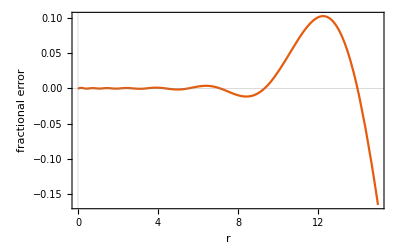

```mathematica
Plot[{Normal[nmcw]/(fWS[r])-1},{r,0,15},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"r","fractional error"}]
```

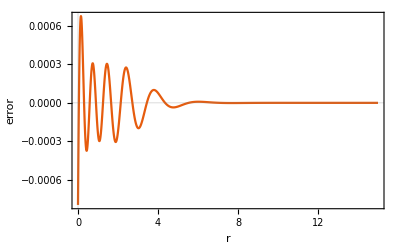

```mathematica
Plot[{Normal[nmcw]-fWS[r]},{r,0,15},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"r","error"}]
```

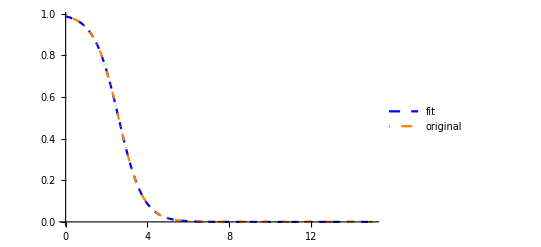

```mathematica
Show[Plot[{Normal[nmcw],fWS[r]},{r,0,15},PlotRange-> Full,PlotLegends->{ "fit","original"},PlotStyle->{{Dashed,Blue},{Orange,DotDashed}}]]
```

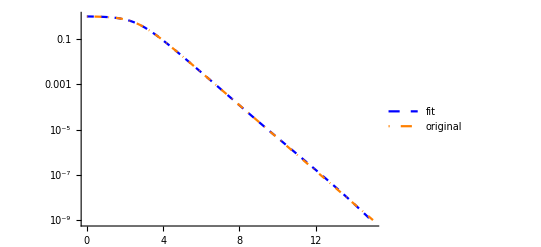

```mathematica
Show[LogPlot[{Normal[nmcw],fWS[r]},{r,0,15},PlotRange-> Full,PlotLegends->{ "fit","original"},PlotStyle->{{Dashed,Blue},{Orange,DotDashed}}]]
```

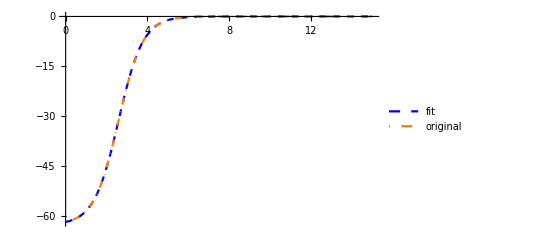

```mathematica
Show[Plot[{V0*Normal[nmcw],V0*fWS[r]},{r,0,15},PlotRange-> Full,PlotLegends->{ "fit","original"},PlotStyle->{{Dashed,Blue},{Orange,DotDashed}}]]
```

```mathematica
imax=12;
tcso=Table[{i,geometric[0.49,4.0,imax,i],cw[i],1/(geometric[0.49,4.0,imax,i])^2,21.00*(-2.0)*cw[i]*1/(geometric[0.49,5.3,imax,i])^2},{i,1,imax}]/.nmcw["BestFitParameters"]//TableForm
```

1 | 0.49 | 0.272822 | 4.16493 | -47.7239
2 | 0.593052 | -1.30687 | 2.84325 | 148.277
3 | 0.717777 | 3.3052 | 1.94098 | -243.235
4 | 0.868733 | -5.6565 | 1.32504 | 269.999
5 | 1.05144 | 6.5652 | 0.904553 | -203.258
6 | 1.27256 | -3.36817 | 0.617505 | 67.636
7 | 1.5402 | -2.43681 | 0.421548 | 31.7389
8 | 1.86412 | 2.63772 | 0.287775 | -22.2835
9 | 2.25616 | 0.718998 | 0.196454 | -3.93975
10 | 2.73065 | 0.234668 | 0.134112 | -0.834026
11 | 3.30494 | 0.0186034 | 0.0915532 | -0.042885
12 | 4. | 0.00107583 | 0.0625 | -0.00160858

```mathematica
(-62.52+39.74)/2
(-62.52-39.74)/2
```

-11.39

-51.13